## Multi-layer system with L-layers and instantaneous Lindblad jump operators L(t)

### Definition of the multi-layer system’s parameters

```mathematica
L=50; (* number of layers *)
y=2; (* coordination number, i.e. number of adiacent layers *)
```

### Solution of the single-layer self-consistency equations

```mathematica
h[i_]:=√((hx)^2+(hz[i])^2);(* effective mean-field magnetic field *)
hz[i_]:=1/y(2 J2 σz[t][[i]]+4 J4 (σz[t][[i]])^3)+ (α J2)/y (If[i>1,σz[t][[i-1]],σz[t][[Length[σxi]]]]+If[i<Length[σxi],σz[t][[i+1]],σz[t][[1]]])+2 (α J4)/y (σz[t][[i]]((If[i>1,σz[t][[i-1]],σz[t][[Length[σxi]]]])^2+(If[i<Length[σxi],σz[t][[i+1]],σz[t][[1]]])^2));
J2=1.; (* two-spin coupling strength *)
J4=1.;(* four-spin coupling strength *)
α=1; (* intra-layer coupling reduction, set it to one (for y=2) in orded to recover the single layer result in the homogeneous periodic boundary condition case *)
β=15.; (* initial temperature *)
tmax=1550; (* maximum integration time *)
hx=2.63; (*transverse magnetic field *)
```

#### P-phase initial conditions from self-consistency equations

```mathematica
β1=β;
σyP=0.;
σzP=0.;
σxP=(Tanh[β1 hx]);
(σxP)^2+(σyP)^2+(σzP)^2;
```

#### F-phase initial conditions from self-consistency equations

```mathematica
σzF=FindRoot[σz-(2J2 σz+4J4(σz)^3)/(√((hx)^2+(2J2(σz)+4J4(σz)^3)^2))Tanh[β √((hx)^2+(2J2(σz)+4J4(σz)^3)^2)],{σz,1}][[1,2]];
σxF=(hx/(√((hx)^2+(2J2(σzF)+4J4(σzF)^3)^2))Tanh[β √((hx)^2+(2J2(σzF)+4J4(σzF)^3)^2)]);
σyF=0.;
hzF=2 J2 σzF+4 J4 (σzF)^3;
hF=√((hx)^2+(hzF)^2);
```

### Definition of the Lindblad parameters

```mathematica
(* Lindblad coupling strengths *)
γbL[i_]:=1/(1+ⅇ^(-β h[i])) 
γL[i_]:=ⅇ^(-2β h[i])/(1+ⅇ^(-β h[i]))
Γ=0.2;

(* Lindblad operators *)
U1x:=0;
U1y:=1;
U1z:=0;
U2x[i_]:=hz[i]/h[i];
U2y:=0;
U2z[i_]:=-hx/h[i];
```

### Initialization of Lindblad’s variables and functions

```mathematica
σxi=Table[If[i<L,σxF,σxP],{i,1,L}];
σyi=Table[If[i<L,σyF,σyP],{i,1,L}];
σzi=Table[If[i<L,σzF,σzP],{i,1,L}];

γ0=Table[If[i==1 || i==L,0,Γ],{i,1,L}];

σx[t_]:=Table[Symbol["σxd"<>ToString@i][t],{i,1,L}];
σy[t_]:=Table[Symbol["σyd"<>ToString@i][t],{i,1,L}];
σz[t_]:=Table[Symbol["σzd"<>ToString@i][t],{i,1,L}];

variables=Join[Table[Symbol["σxd"<>ToString@i],{i,1,L}],Table[Symbol["σyd"<>ToString@i],{i,1,L}],Table[Symbol["σzd"<>ToString@i],{i,1,L}]];

p[i_]:=If[i==L || i==1,0,1];

(* we have a differential equation for each layer *)
(* we write the explicit equation for each component of the magnetization *)
listequation=Table[{
σx'[t][[i]]==p[i](2 hz[i] σy[t][[i]])
+4γ0[[i]](γL[i]+γbL[i])
 ((U1x U1x+U2x[i] U2x[i]-2)σx[t][[i]]
+(U1y U1x+U2y U2x[i])σy[t][[i]]
+(U1z U1x+U2z[i] U2x[i])σz[t][[i]])
+8γ0[[i]](γL[i]-γbL[i])(U1y U2z[i]-U1z U2y),
σy'[t][[i]]==p[i](2hx σz[t][[i]]-2 hz[i] σx[t][[i]])
+4γ0[[i]](γL[i]+γbL[i])
 ((U1x U1y+U2x[i] U2y)σx[t][[i]]
+(U1y U1y+U2y U2y-2)σy[t][[i]]
+(U1z U1y+U2z[i] U2y)σz[t][[i]])
+8γ0[[i]](γL[i]-γbL[i])(U1z U2x[i]-U1x U2z[i]),
σz'[t][[i]]==-p[i](2 hx σy[t][[i]])
+4γ0[[i]](γL[i]+γbL[i])
 ((U1x U1z+U2x[i] U2z[i])σx[t][[i]]
+(U1y U1z+U2y U2z[i])σy[t][[i]]
+(U1z U1z+U2z[i] U2z[i]-2)σz[t][[i]])
+8γ0[[i]](γL[i]-γbL[i])(U1x U2y-U1y U2x[i]),

σx[0][[i]]==σxi[[i]],σy[0][[i]]==σyi[[i]],σz[0][[i]]==σzi[[i]]},{i,1,Length[σxi]}]//Flatten;
```

### Solution of the differential equation for the magnetization components

```mathematica
s=NDSolve[listequation,variables,{t,0,tmax}]; (* Lindblad Equation solver *)
```

### Printing results

```mathematica
Evaluate[σz[0]/.s]//Flatten
Evaluate[σz[tmax]/.s]//Flatten
```

{0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.}

{0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836405,0.836402,0.836389,0.836329,0.836043,0.834697,0.828389,0.79968,0.68477,0.397114,0.154981,0.053438,0.0164226,0.}

### Plots of the wetting profile

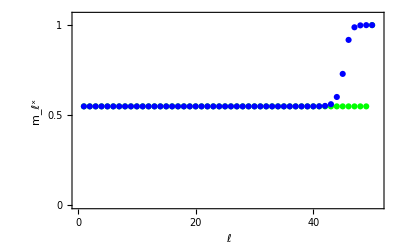

```mathematica
Show[{ListPlot[Evaluate[σx[0]/.s],PlotStyle->Green,PlotRange->{{0,51},{0,1.05}}],ListPlot[Evaluate[σx[tmax]/.s],PlotStyle->Blue]},Frame->True,FrameStyle->Directive[Thick,Black],RotateLabel->False,PlotStyle->Thick,FrameTicks->{{{0,0.5,1},{0,0.5,1}},{{0,10,20,30,40,50},{0,10,20,30,40,50}}},FrameLabel->{Style["ℓ",25,FontFamily->Times],Style[Subsuperscript["m","ℓ","x"],25,FontFamily->"Times"]},LabelStyle->Medium]
```

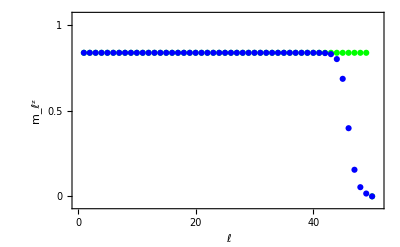

```mathematica
Show[{ListPlot[Evaluate[σz[0]/.s],PlotStyle->Green,PlotRange->{{0,51},{-0.05,1.05}}],ListPlot[Evaluate[σz[tmax]/.s],PlotStyle->Blue]},Frame->True,FrameStyle->Directive[Thick,Black],RotateLabel->False,PlotStyle->Thick,FrameTicks->{{{0,0.5,1},{0,0.5,1}},{{0,10,20,30,40,50},{0,10,20,30,40,50}}},FrameLabel->{Style["ℓ",25,FontFamily->Times],Style[Subsuperscript["m","ℓ","z"],25,FontFamily->"Times"]},LabelStyle->Medium]
```

### Plots of the magnetization as a function of time

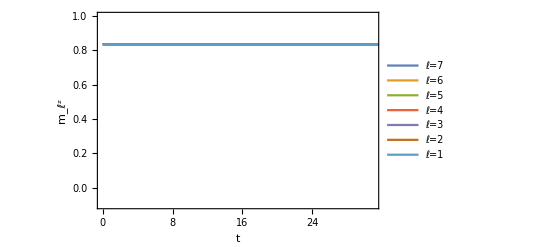

```mathematica
(* first seven layers *)
Plot[Evaluate[{σz[t][[1]],σz[t][[2]],σz[t][[3]],σz[t][[4]],σz[t][[5]],σz[t][[6]],σz[t][[7]]}/.s],{t,0,tmax},PlotRange->{{0,0.02*tmax},{-0.1,1}},Frame->True,FrameStyle->Directive[Thick,Black],RotateLabel->False,PlotStyle->Thick,FrameLabel->{Style["t",25,FontFamily->Times],Style[Subsuperscript["m","ℓ","z"],25,FontFamily->"Times"]},LabelStyle->Medium,PlotLegends->{Style["ℓ=7",18,FontFamily->"Times"],Style["ℓ=6",18,FontFamily->"Times"],Style["ℓ=5",18,FontFamily->"Times"],Style["ℓ=4",18,FontFamily->"Times"],Style["ℓ=3",18,FontFamily->"Times"],Style["ℓ=2",18,FontFamily->"Times"],Style["ℓ=1
",18,FontFamily->"Times"]}]
```

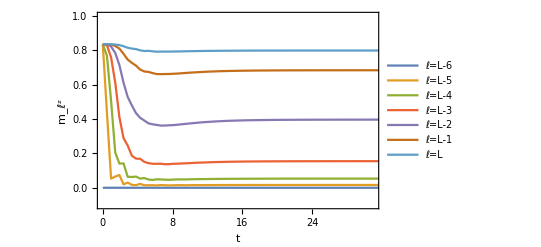

```mathematica
(* last seven layers *)
Plot[Evaluate[{σz[t][[L]],σz[t][[L-1]],σz[t][[L-2]],σz[t][[L-3]],σz[t][[L-4]],σz[t][[L-5]],σz[t][[L-6]]}/.s],{t,0,tmax},PlotRange->{{0,0.02*tmax},{-0.1,1}},Frame->True,FrameStyle->Directive[Thick,Black],RotateLabel->False,PlotStyle->Thick,FrameLabel->{Style["t",25,FontFamily->Times],Style[Subsuperscript["m","ℓ","z"],25,FontFamily->"Times"]},LabelStyle->Medium,PlotLegends->{Style["ℓ=L-6",18,FontFamily->"Times"],Style["ℓ=L-5",18,FontFamily->"Times"],Style["ℓ=L-4",18,FontFamily->"Times"],Style["ℓ=L-3",18,FontFamily->"Times"],Style["ℓ=L-2",18,FontFamily->"Times"],Style["ℓ=L-1",18,FontFamily->"Times"],Style["ℓ=L
",18,FontFamily->"Times"]}]
```

### Plots of the single-layer and multi-layer energies in time

```mathematica
En0=-hx Tanh[β hx]; (* energy of the P phase *)
Enp=-J2/1 (σzF)^2-J4/1 (σzF)^4-hx σxF; (* energy of the F phase *)
En[i_]:=-J2/1 (σz[t][[i]])^2-J4/1 (σz[t][[i]])^4-hx σx[t][[i]]; (* energy of the disconnnected layer i *)
Enc[i_]:=-J2/y (σz[t][[i]])^2-J2/(2y) (σz[t][[i]]σz[t][[i-1]]+σz[t][[i]]σz[t][[i+1]])-J4/y (σz[t][[i]])^4-J4/(2y) (σz[t][[i]])^2((σz[t][[i-1]])^2+(σz[t][[i+1]])^2)-hx σx[t][[i]]; (* energy of the embedded layer i *)
EnL:=-J2/y (σz[t][[L]])^2-J2/(2y) (σz[t][[L]]σz[t][[L]]+σz[t][[L]]0)-J4/y (σz[t][[L]])^4-J4/(2y) (σz[t][[L]])^2((σz[t][[L]])^2+0)-hx σx[t][[L]]; (* energy of the embedded layer L *)
En1:=-J2/y (σz[t][[1]])^2-J2/(2y) (σz[t][[1]]σzF+σz[t][[1]]σz[t][[2]])-J4/y (σz[t][[1]])^4-J4/(2y) (σz[t][[1]])^2((σzF)^2+(σz[t][[2]])^2)-hx σx[t][[1]]; (* energy of the embedded layer 1 *)
```

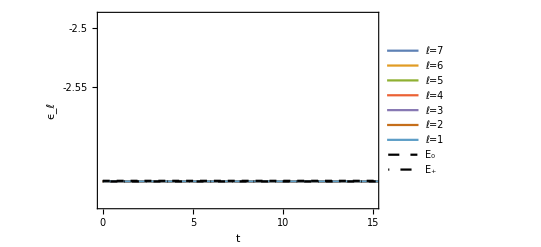

```mathematica
(* first seven layers *)
allP=Plot[Evaluate[{Enc[7],Enc[6],Enc[5],Enc[4],Enc[3],Enc[2],En1,En0,Enp}/.s],{t,0,0.1tmax},PlotRange->{{0,15},{Min[Enp,En0]-0.02,Max[Enp,En0]+0.14}},PlotStyle->{,,,,,,,{Dashed,Black},{DotDashed,Black}},Frame->True,FrameStyle->Directive[Thick,Black],RotateLabel->False,PlotStyle->Thick,FrameTicks->{{{-2.55,-2.50,-2.45,-2.40},{-2.55,-2.50,-2.45,-2.40}},{{0,5,10,15},{0,5,10,15}}},PlotLegends->{Style["ℓ=7",18,FontFamily->"Times"],Style["ℓ=6",18,FontFamily->"Times"],Style["ℓ=5",18,FontFamily->"Times"],Style["ℓ=4",18,FontFamily->"Times"],Style["ℓ=3",18,FontFamily->"Times"],Style["ℓ=2",18,FontFamily->"Times"],Style["ℓ=1
",18,FontFamily->"Times"],Style["E_0",18,FontFamily->"Times"],Style["E_+",18,FontFamily->"Times"]},FrameLabel->{Style["t",20],Style[Subscript["ϵ","ℓ"],25,FontFamily->"Times"]},LabelStyle->Medium]
```

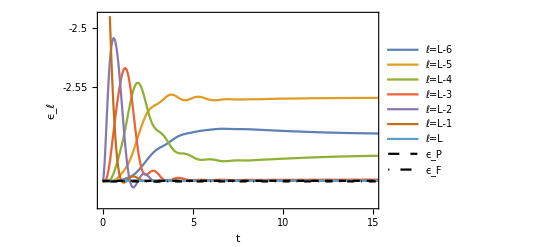

```mathematica
(* last seven layers *)
allF=Plot[Evaluate[{Enc[L-6],Enc[L-5],Enc[L-4],Enc[L-3],Enc[L-2],Enc[L-1],EnL,En0,Enp}/.s],{t,0,0.1tmax},PlotRange->{{0,15},{Min[Enp,En0]-0.02,Max[Enp,En0]+0.14}},PlotStyle->{,,,,,,,{Dashed,Black},{DotDashed,Black}},Frame->True,FrameStyle->Directive[Thick,Black],RotateLabel->False,PlotStyle->Thick,FrameTicks->{{{-2.55,-2.50,-2.45,-2.40},{-2.55,-2.50,-2.45,-2.40}},{{0,5,10,15},{0,5,10,15}}},PlotLegends->{Style["ℓ=L-6",18,FontFamily->"Times"],Style["ℓ=L-5",18,FontFamily->"Times"],Style["ℓ=L-4",18,FontFamily->"Times"],Style["ℓ=L-3",18,FontFamily->"Times"],Style["ℓ=L-2",18,FontFamily->"Times"],Style["ℓ=L-1",18,FontFamily->"Times"],Style["ℓ=L
",18,FontFamily->"Times"],Style["ϵ_P",18,FontFamily->"Times"],Style["ϵ_F",18,FontFamily->"Times"]},FrameLabel->{Style["t",20],Style[Subscript["ϵ","ℓ"],25,FontFamily->"Times"]},LabelStyle->Medium]
```

### Plots of the energy profile

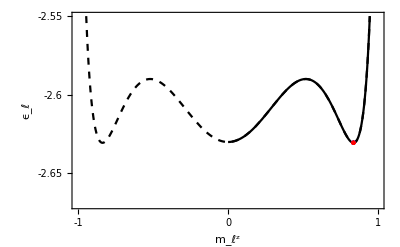

```mathematica
(* first seven layers *)
a1=Evaluate[{En1,Enc[2],Enc[3],Enc[4],Enc[5],Enc[6],Enc[7]}/.s/.t->tmax]//Flatten;
a1b=Evaluate[{En[1],En[2],En[3],En[4],En[5],En[6],En[7]}/.s/.t->tmax]//Flatten;
a2=Evaluate[{σz[t][[1]],σz[t][[2]],σz[t][[3]],σz[t][[4]],σz[t][[5]],σz[t][[6]],σz[t][[7]]}/.s/.t->tmax]//Flatten;

Plot[{(-J2/1 (x)^2-J4/1 (x)^4-hx Sqrt[1-x^2])HeavisideTheta[x],-J2/1 (x)^2-J4/1 (x)^4-hx Sqrt[1-(x)^2]},{x,-1,1},PlotRange->{{-1,1},{-2.67,-2.55}},PlotStyle->{{Black},{Black,Dashed}},Epilog->{{Blue,PointSize@Large,Point[{a2[[1]],a1b[[1]]}]},{Blue,PointSize@Large,Point[{a2[[2]],a1b[[2]]}]},{Blue,PointSize@Large,Point[{a2[[3]],a1b[[3]]}]},{Blue,PointSize@Large,Point[{a2[[4]],a1b[[4]]}]},{Blue,PointSize@Large,Point[{a2[[5]],a1b[[5]]}]},{Blue,PointSize@Large,Point[{a2[[6]],a1b[[6]]}]},{Blue,PointSize@Large,Point[{a2[[7]],a1b[[7]]}]},{Red,PointSize@Medium,Point[{a2[[1]],a1[[1]]}]},{Red,PointSize@Medium,Point[{a2[[2]],a1[[2]]}]},{Red,PointSize@Medium,Point[{a2[[3]],a1[[3]]}]},{Red,PointSize@Medium,Point[{a2[[4]],a1[[4]]}]},{Red,PointSize@Medium,Point[{a2[[5]],a1[[5]]}]},{Red,PointSize@Medium,Point[{a2[[6]],a1[[6]]}]},{Red,PointSize@Medium,Point[{a2[[7]],a1[[7]]}]}},Frame->True,FrameStyle->Directive[Thick,Black],RotateLabel->False,PlotStyle->Thick,FrameTicks->{{{-2.55,-2.60,-2.65},{-2.60,-2.55,-2.65}},{{-1,0,1},{-1,0,1}}},FrameLabel->{Style[Subsuperscript["m","ℓ","z"],25,FontFamily->"Times"],Style[Subscript["ϵ","ℓ"],25,FontFamily->"Times"]},LabelStyle->Medium,Axes->False]
```

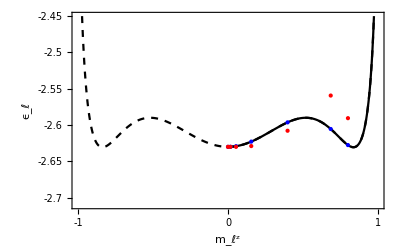

```mathematica
(* last seven layers *)
a1=Evaluate[{Enc[L-6],Enc[L-5],Enc[L-4],Enc[L-3],Enc[L-2],Enc[L-1],EnL}/.s/.t->tmax]//Flatten;
a1b=Evaluate[{En[L-6],En[L-5],En[L-4],En[L-3],En[L-2],En[L-1],En[L]}/.s/.t->tmax]//Flatten;
a2=Evaluate[{σz[t][[L-6]],σz[t][[L-5]],σz[t][[L-4]],σz[t][[L-3]],σz[t][[L-2]],σz[t][[L-1]],0}/.s/.t->tmax]//Flatten;

Plot[{(-J2/1 (x)^2-J4/1 (x)^4-hx Sqrt[1-x^2])HeavisideTheta[x],-J2/1 (x)^2-J4/1 (x)^4-hx Sqrt[1-(x)^2]},{x,-1,1},PlotRange->{{-1,1},{-2.71,-2.45}},PlotStyle->{{Black},{Black,Dashed}},Epilog->{{Blue,PointSize@Large,Point[{a2[[1]],a1b[[1]]}]},{Blue,PointSize@Large,Point[{a2[[2]],a1b[[2]]}]},{Blue,PointSize@Large,Point[{a2[[3]],a1b[[3]]}]},{Blue,PointSize@Large,Point[{a2[[4]],a1b[[4]]}]},{Blue,PointSize@Large,Point[{a2[[5]],a1b[[5]]}]},{Blue,PointSize@Large,Point[{a2[[6]],a1b[[6]]}]},{Blue,PointSize@Large,Point[{a2[[7]],a1b[[7]]}]},{Red,PointSize@Medium,Point[{a2[[1]],a1[[1]]}]},{Red,PointSize@Medium,Point[{a2[[2]],a1[[2]]}]},{Red,PointSize@Medium,Point[{a2[[3]],a1[[3]]}]},{Red,PointSize@Medium,Point[{a2[[4]],a1[[4]]}]},{Red,PointSize@Medium,Point[{a2[[5]],a1[[5]]}]},{Red,PointSize@Medium,Point[{a2[[6]],a1[[6]]}]},{Red,PointSize@Medium,Point[{a2[[7]],a1[[7]]}]}},Frame->True,FrameStyle->Directive[Thick,Black],RotateLabel->False,PlotStyle->Thick,FrameTicks->{{{-2.7,-2.65,-2.60,-2.55,-2.50,-2.45},{-2.7,-2.65,-2.60,-2.55,-2.50,-2.45}},{{-1,0,1},{-1,0,1}}},FrameLabel->{Style[Subsuperscript["m","ℓ","z"],25,FontFamily->"Times"],Style[Subscript["ϵ","ℓ"],25,FontFamily->"Times"]},LabelStyle->Medium,Axes->False]
```

### Plot of total energies as a function of time

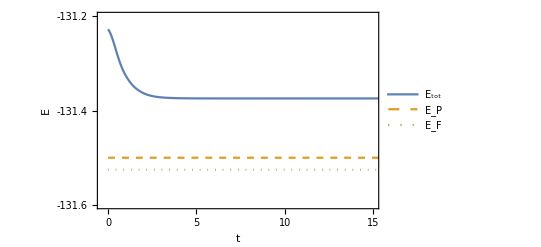

```mathematica
totalenergy=Plot[{Evaluate[{En1+EnL+Sum[Enc[i],{i,2,L-1}]}/.s],En0*L,Enp*L},{t,0,0.01tmax},PlotRange->{{-0.3,15},{-131.6,-131.2}},PlotStyle->{{},{Dashed},{Dotted}},PlotLegends->{Style["E_tot",18,FontFamily->"Times"],Style["E_P",18,FontFamily->"Times"],Style["E_F",18,FontFamily->"Times"]},Frame->True,FrameStyle->Directive[Thick,Black],FrameTicks->{{0,5,10,15},{-131.6,-131.4,-131.2}},RotateLabel->False,PlotStyle->Thick,FrameLabel->{Style["t",20],Style["E",20]}]
```